## Function for reversing Y-axis

```mathematica
ReverseY[arg_Graphics]:=Module[{original,newPlot,newPoint,count,newOrigin,newTick,plotRange,oldAxe },
original=arg;
Catch@Which[Count[original,_GraphicsComplex,Infinity]>0,
newPlot=Replace[original,GraphicsComplex[list_,y__]:>GraphicsComplex[newPoint=Times[{1,-1},#]&/@list,y],Infinity],

(count=Count[original,_Point,Infinity])>0,
newPlot=Replace[original,Point[list_]:>Point[Times[{1,-1},#]&/@list],Infinity];
newPoint=Cases[Cases[original,Point[list_]:>list,Infinity],{x_?NumericQ,y_?NumericQ}:>{x,-y},Infinity],

(count=Count[original,_Line,Infinity])>0,
newPlot=Replace[original,Line[list_]:>Line[Times[{1,-1},#]&/@list],Infinity];
newPoint=Cases[Cases[original,Line[list_]:>list,Infinity],{x_?NumericQ,y_?NumericQ}:>{x,-y},Infinity],

True,Throw[$Failed]];

newOrigin=Which[Plus@@@(PlotRange/.AbsoluteOptions[original,PlotRange])=={0,0}||(Plus@@@(PlotRange/.AbsoluteOptions[original,PlotRange]))[[1]]==0,{0,0},(AxesOrigin/.AbsoluteOptions[original,AxesOrigin])=={0,0} ,{0,Last[Min/@Transpose[newPoint]]},True,Min/@Transpose[newPoint]];
Off[NumberForm::"iprf"];
newTick=ReplacePart[AbsoluteOptions[original,Ticks][[1]],{2,2}->(AbsoluteOptions[original,Ticks][[1,2,2]]/.{x_?NumericQ,y__}:>{-x,y})];
plotRange=MapAt[-1 #&,AbsoluteOptions[original,PlotRange][[1]],{2,2}];
Show[newPlot,AxesOrigin->newOrigin,newTick,plotRange]]
```

## Code

```mathematica
Print[tephigram method: using an ambient sounding to provide a simplistic thermohydrostatic/cyclostrophic estimate of peak achievable intensity for a tropical storm and hurricane spawned in that environment; without EventLocator]
```

EventLocator without

```mathematica
pambs:=101500.;
tambs:=299.0;
rhoambs:=pambs/(287.1*tambs);
pinterface1:=80000.0;
```

```mathematica
rheyed:=0.65
```

```mathematica
rhamb=Interpolation[{{101500,0.84},{100000,0.81},{95000,0.81},{90000,0.79},{85000,0.74},{80000,0.70},{75000,0.64},{70000,0.60},{65000,0.56},{60000,0.54},{55000,0.51},{50000,0.49},{45000,0.45},{40000,0.44},{30000,0.39},{20000,0.37},{10000,0.35}},InterpolationOrder->1];
```

```mathematica
tamb=Interpolation[{{101500,299},{100000,299},{95000,296},{90000,293},{85000,290},{80000,288},{75000,285},{70000,282},{65000,278},{60000,274},{55000,271},{50000,266},{45000,261},{40000,255},{30000,240},{20000,218},{10000,210}}];
```

```mathematica
Print[StringForm ["pambs = `` [Pa], tambs = `` [K], rhoambs = `` [kg/m^3], pinterface1 = `` [Pa], rheyed = `` [dimensionless]",Sequence@@(StandardForm/@{pambs,tambs,rhoambs,pinterface1, rheyed})]]
```

pambs = StandardForm`101500.` [Pa], tambs = StandardForm`299.` [K], rhoambs = StandardForm`1.1823924867403128` [kg/m^3], pinterface1 = StandardForm`80000.` [Pa], rheyed = StandardForm`0.65` [dimensionless]

```mathematica
rhoamb[p_]:=p/(287.1*tamb[p]);
```

```mathematica
pvsat[t_]:=610.78*Exp[a[t]*(t-273.16)/(t-b[t])];
```

```mathematica
Clear[a,b]
```

```mathematica
a[t_]:=If[t>273.16,17.2693882,21.8745584];
b[t_]:=If[t>273.16,35.86,7.66];
```

```mathematica
pvamb[p_]:=rhamb[p]*pvsat[tamb[p]];
```

```mathematica
rhovamb[p_]:=0.622*pvamb[p]/(287.1*tamb[p]);
```

```mathematica
dpvsatdt[t_]:=(pvsat[t])*(a[t])*(273.16-b[t])/(t-b[t])^2;
```

```mathematica
yamb[p_]:=rhovamb[p]/rhoamb[p];
```

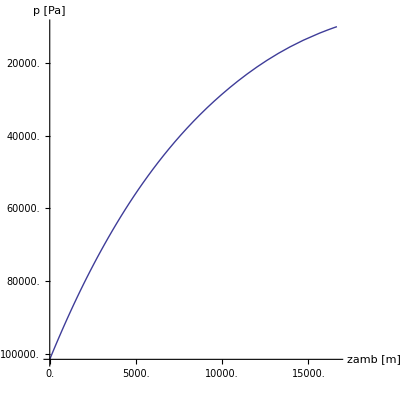

```mathematica
sol= NDSolve[{D[zamb[p],p]==-1/(9.8*rhoamb[p]),zamb[pambs]==0},zamb,{p,pambs,10000},MaxStepSize->100,StartingStepSize->100];

ParametricPlot[{Evaluate[zamb[p]/.sol[[1]],p]},{p,pambs,10000},AxesLabel->{"zamb [m]","p [Pa]"},AxesOrigin->{0,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}]}]//ReverseY
```

```mathematica
tswitch= t/.FindRoot[pvsat[t]/((t/tambs)^3.5)==(rhamb[pambs])*(pvsat[tambs]),{t,315,200}]
```

295.385

```mathematica
pswitch:=pambs*(tswitch/tambs)^3.5
```

```mathematica
Print[StringForm["pLCL = `` [Pa], TLCL = `` [K]",Sequence@@(StandardForm/@{pswitch,tswitch})]]
```

pLCL = StandardForm`97269.47095929731` [Pa], TLCL = StandardForm`295.38502706181663` [K]

```mathematica
pdiff[p_,pambs_,tswitch_,tambs_]:=(pswitch)-p
```

```mathematica
sol1=NDSolve[{D[tmoist1[p],p]==((287.1*tmoist1[p])/p+2.5*10^6*0.622*(pvsat[tmoist1[p]])/p^2)/(1004+2.5*10^6*0.622*dpvsatdt[tmoist1[p]]/p),tmoist1[pswitch]==tswitch},tmoist1,{p,pswitch,10000},MaxStepSize->100,StartingStepSize->100]
```

{{tmoist1→InterpolatingFunction[{{10000.,97269.5}},<>]}}

```mathematica
ptrop=p/.FindRoot[(tmoist1[p]/.sol1[[1]])-tamb[p]==0,{p,10000,50000}]
```

18935.5

```mathematica
ttrop:=tamb[ptrop];
```

```mathematica
ztrop:=zamb[ptrop]/.sol[[1]];
rhotrop:=rhoamb[ptrop];
```

```mathematica
Print[StringForm["ztrop = `` [m], ptrop = `` [Pa], ttrop = `` [K], rhotrop = `` [kg/m^3]",Sequence@@(StandardForm/@{ztrop,ptrop,ttrop,rhotrop})]]
```

ztrop = StandardForm`12705.564874310228` [m], ptrop = StandardForm`18935.54224437548` [Pa], ttrop = StandardForm`216.11428944323038` [K], rhotrop = StandardForm`0.30518351475412775` [kg/m^3]

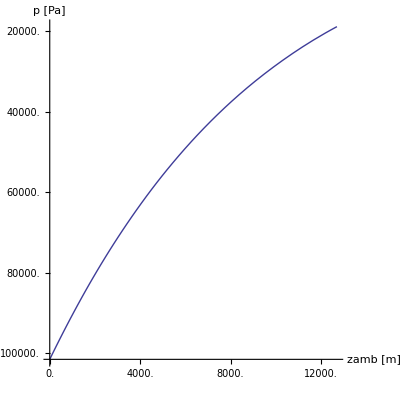

```mathematica
pza=ParametricPlot[{Evaluate[zamb[p]/.sol[[1]],p]},{p,pambs,ptrop}, AxesLabel->{"zamb [m]","p [Pa]"},AxesOrigin->{0,10000},PlotRange->All, AspectRatio->1,PlotStyle->{Dashing[{}]}];
pza//ReverseY
```

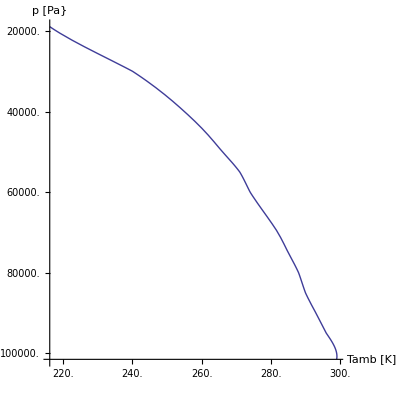

```mathematica
pta=ParametricPlot[{Evaluate[tamb[p],p]},{p,pambs,ptrop},AxesLabel->{"Tamb [K]","p [Pa}"}, AxesOrigin->{200,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}]}];
pta//ReverseY
```

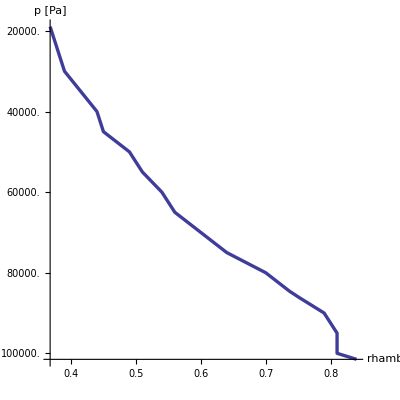

```mathematica
prha=ParametricPlot[{Evaluate[rhamb[p],p]},{p,pambs,ptrop},AxesLabel->{"rhamb","p [Pa]"},AxesOrigin->{0,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}],Thickness[0.006]}];
prha//ReverseY
```

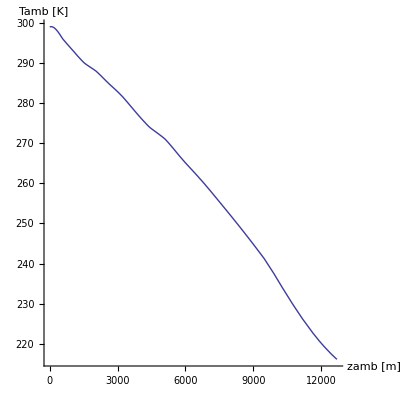

```mathematica
taza=ParametricPlot[Evaluate[{zamb[p]/.sol[[1]],tamb[p]}],{p,ptrop,pambs},AxesLabel->{"zamb [m]","Tamb [K]"},AxesOrigin->{0,200},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}]}]
```

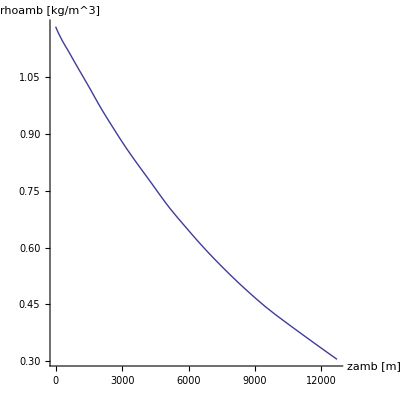

```mathematica
rhoaza=ParametricPlot[Evaluate[{zamb[p]/.sol[[1]],rhoamb[p]}],{p,ptrop,pambs},AxesOrigin->{0,0},AxesLabel->{"zamb [m]","rhoamb [kg/m^3]"},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}]}]
```

```mathematica
solm=NDSolve[{D[zmoist[p],p]==-287.1*tmoist[p]/(9.8*p),D[tmoist[p],p]==((287.1*tmoist[p])/p +UnitStep[pdiff[p,pambs,tswitch,tambs]]*2.5*10^6*0.622*(pvsat[tmoist[p]])/p^2)/(1004+UnitStep[pdiff[p,pambs,tswitch,tambs]]*2.5*10^6*0.622*(dpvsatdt[tmoist[p]])/p),tmoist[ptrop]==ttrop,zmoist[ptrop]==ztrop},{zmoist,tmoist},{p,ptrop,pambs},MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity]
```

{{zmoist→InterpolatingFunction[{{18935.5,101500.}},<>],tmoist→InterpolatingFunction[{{18935.5,101500.}},<>]}}

```mathematica
pmoists:=p/. FindRoot[(zmoist[p]/.solm[[1,1]])==0,{p,pambs,90000}]
```

```mathematica
rhomoist[p_]:=p/(287.1*tmoist[p]/.solm[[1,2]]);
```

```mathematica
rhmoist[p_]:=If[p>pswitch,(p/pswitch)*(pvsat[tswitch])/(pvsat[tmoist[p]/.solm[[1,2]]]),1];
```

```mathematica
ymoist[p_]:=0.622*(rhmoist[p])*(pvsat[tmoist[p]/.solm[[1,2]]])/p;
```

```mathematica
tmoists:=tmoist[pmoists]/.solm[[1,2]];rhomoists:=pmoists/(287.1*tmoists);rhmoists:=rhmoist[pmoists];
```

```mathematica
Print[StringForm["pmoists = `` [Pa], tmoists = `` [K], rhomoists = `` [kg/m^3], rhmoists = `` [dimensionless]",Sequence@@(StandardForm/@{pmoists,tmoists,rhomoists,rhmoists})]]
```

pmoists = StandardForm`99823.25835893511` [Pa], tmoists = StandardForm`297.582206104238` [K], rhomoists = StandardForm`1.1684001125437942` [kg/m^3], rhmoists = StandardForm`0.8988434831567473` [dimensionless]

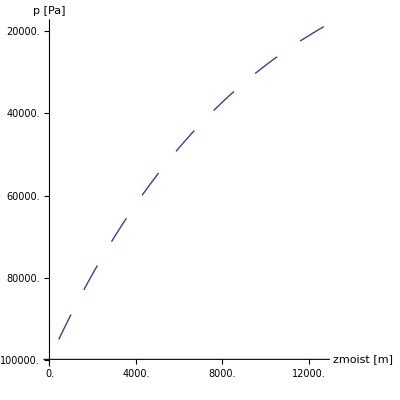

```mathematica
pzm=ParametricPlot[Evaluate[{zmoist[p]/.solm[[1,1]],p}],{p,pmoists,ptrop},AxesLabel->{"zmoist [m]","p [Pa]"},AxesOrigin->{0,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.05,0.05}]}];
pzm//ReverseY
```

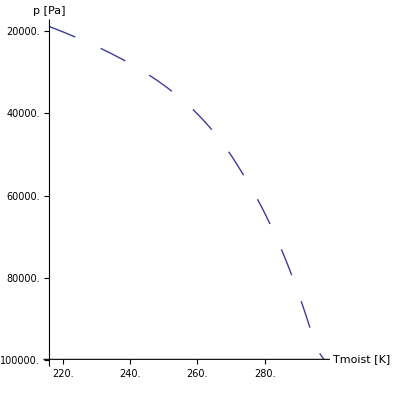

```mathematica
ptm=ParametricPlot[Evaluate[{tmoist[p]/.solm[[1,2]],p}],{p,pmoists,ptrop},AxesLabel->{"Tmoist [K]","p [Pa]"},AxesOrigin->{200,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.05,0.05}]}];
ptm//ReverseY
```

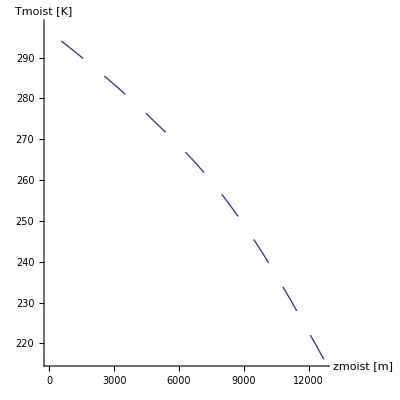

```mathematica
tmzm=ParametricPlot[Evaluate[{zmoist[p]/.solm[[1,1]],tmoist[p]/.solm[[1,2]]}],{p,ptrop,pmoists},AxesLabel->{"zmoist [m]","Tmoist [K]"},AxesOrigin->{0,200},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.05,0.05}]}]
```

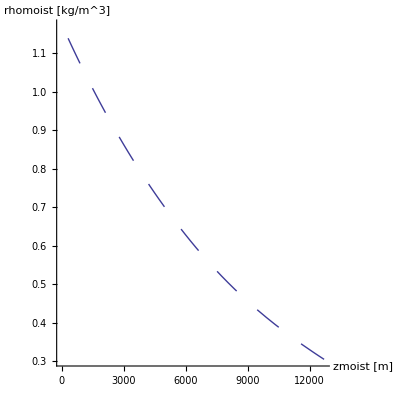

```mathematica
rhomzm=ParametricPlot[Evaluate[{zmoist[p]/.solm[[1,1]],rhomoist[p]}],{p,ptrop,pmoists},AxesLabel->{"zmoist [m]","rhomoist [kg/m^3]"},AxesOrigin->{0,0},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.05,0.05}]}]
```

```mathematica
sole=NDSolve[{D[zeyed[p],p]==-(287.1*teyed[p])/(9.8*p),D[teyed[p],p]==(((287.1*teyed[p])/p)+(rheyed*2.5*10^6*0.622*(pvsat[teyed[p]])/p^2))/(1004+(rheyed*2.5*10^6*0.622*(dpvsatdt[teyed[p]])/p)),teyed[ptrop]==ttrop,zeyed[ptrop]==ztrop},{zeyed,teyed},{p,ptrop,pmoists},MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity]
```

{{zeyed→InterpolatingFunction[{{18935.5,99823.3}},<>],teyed→InterpolatingFunction[{{18935.5,99823.3}},<>]}}

```mathematica
peyeds=p/.FindRoot[(zeyed[p]/.sole[[1,1]])==0,{p,20000,pmoists}];
```

```mathematica
yeyed[p_]:=rheyed*0.622*(pvsat[(teyed[p]/.sole[[1,2]])])/p;
```

```mathematica
rhoeyed[p_]:=p/(287.1*(teyed[p]/.sole[[1,2]]));
```

```mathematica
teyeds:=teyed[peyeds]/.sole[[1,2]];
```

```mathematica
rhoeyeds:=rhoeyed[peyeds];
```

```mathematica
yeyeds:=yeyed[peyeds];
```

```mathematica
Print[StringForm["peyeds = `` [Pa], teyeds = `` [K], rhoeyeds = `` [kg/m^3], yeyeds = `` [dimensionless]",Sequence@@(StandardForm/@{peyeds,teyeds,rhoeyeds, yeyeds})]]
```

peyeds = StandardForm`98532.88346042893` [Pa], teyeds = StandardForm`301.2945449637154` [K], rhoeyeds = StandardForm`1.13908656856527` [kg/m^3], yeyeds = StandardForm`0.015630198692780876` [dimensionless]

```mathematica
pinterface:=If[pinterface1<peyeds,pinterface1,peyeds]
```

```mathematica
Print[StringForm["pinterface1 = `` [Pa], peyeds = `` [Pa], pinterface = `` [Pa]",Sequence@@(StandardForm/@{pinterface1, peyeds, pinterface})]]
```

pinterface1 = StandardForm`80000.` [Pa], peyeds = StandardForm`98532.88346042893` [Pa], pinterface = StandardForm`80000.` [Pa]

```mathematica
factor:=If[pinterface>pswitch,0,1];
```

```mathematica
zeyedi:=zeyed[pinterface]/.sole[[1,1]];
```

```mathematica
teyemi=t/.FindRoot[t+9.8*(zeyedi)/1004 +(factor*(0.622)*(2.5*10^6)/(1004))*(pvsat[t])/pinterface+(1-factor)*((0.622)*(2.5*10^6)/(1004))*(pvsat[tswitch])/pswitch==ttrop+9.8*ztrop/1004+((rheyed*0.622*2.5*10^6)/(1004))*pvsat[ttrop]/ptrop,{t,320,ttrop}]
```

288.582

```mathematica
solem=NDSolve[{D[zeyem[p],p]==-287.1*teyem[p]/(9.8*p),D[teyem[p],p]==((287.1*teyem[p])/p+UnitStep[pdiff[p,pambs,tswitch,tambs]]*0.622*2.5*10^6*(pvsat[teyem[p]])/p^2)/(1004+UnitStep[pdiff[p,pambs,tswitch,tambs]]*0.622*2.5*10^6*(dpvsatdt[teyem[p]])/p),zeyem[pinterface]==zeyedi,teyem[pinterface]==teyemi},{zeyem,teyem},{p,pinterface,pmoists},MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity]
```

{{zeyem→InterpolatingFunction[{{80000.,99823.3}},<>],teyem→InterpolatingFunction[{{80000.,99823.3}},<>]}}

```mathematica
rhoeyem[p_]:=p/(287.1*(teyem[p]/.solem[[1,2]]))
```

```mathematica
yeyem[p_]:=If[p<pswitch,0.622*(pvsat[(teyem[p]/.solem[[1,2]])])/p,0.622*pvsat[tswitch]/pswitch]
```

```mathematica
rhoeye[p_]:=If[p<pinterface,rhoeyed[p],rhoeyem[p]];
```

```mathematica
peyedi:=pinterface;
```

```mathematica
teyedi:=teyed[pinterface]/.sole[[1,2]];
```

```mathematica
rhoeyedi:= rhoeyed[pinterface];
```

```mathematica
yeyedi:=yeyed[pinterface];
```

```mathematica
Print[StringForm["The height of the eye's dry/moist interface is `` [m].",StandardForm@zeyedi]]
```

The height of the eye's dry/moist interface is StandardForm`1814.4453343576226` [m].

```mathematica
Print[StringForm["peyedi (i.e., pinterface) = `` [Pa], teyedi = `` [K], rhoeyedi = `` [kg/m^3], yeyedi = `` [dimensionless]",Sequence@@(StandardForm/@{peyedi, teyedi, rhoeyedi, yeyedi})]]
```

peyedi (i.e., pinterface) = StandardForm`80000.` [Pa], teyedi = StandardForm`293.13197824141207` [K], rhoeyedi = StandardForm`0.9505907754668083` [kg/m^3], yeyedi = StandardForm`0.011795659777778777` [dimensionless]

```mathematica
teye[p_]:=If[p<pinterface,(teyed[p]/.sole[[1,2]]),(teyem[p]/.solem[[1,2]])];
```

```mathematica
yeye[p_]:=If[p<pinterface,yeyed[p],yeyem[p]]
```

```mathematica
zeye[p_]:=If[p<pinterface,(zeyed[p]/.sole[[1,1]]),(zeyem[p]/.solem[[1,1]])];
```

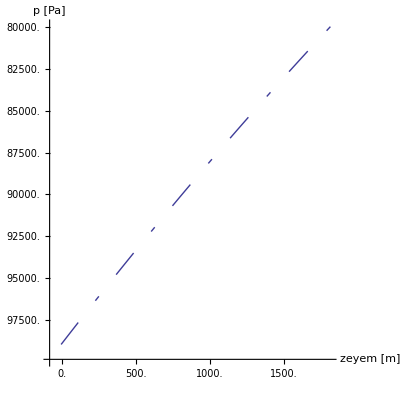

```mathematica
ParametricPlot[Evaluate[{zeyem[p]/.solem[[1,1]],p}],{p,pinterface,pmoists},AxesOrigin->{0,pmoists},AxesLabel->{"zeyem [m]","p [Pa]"}, PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.01,0.05,0.05,0.05}]}]//ReverseY
```

```mathematica
peyems:=p/.FindRoot[(zeyem[p]/.solem[[1,1]])==0,{p,pinterface,pmoists}]
teyems:=teyem[peyems]/.solem[[1,2]];
rhoeyems:=rhoeyem[peyems];
```

```mathematica
zeyems:=zeyem[peyems]/.solem[[1,1]]
```

```mathematica
Print[StringForm["zeyems = `` [m]",StandardForm@zeyems]]
```

zeyems = StandardForm`3.6007655190850585`*^-13 [m]

```mathematica
Print[StringForm["peyems = `` [Pa], teyems = `` [K], rhoeyems = `` [kg/m^3]",Sequence@@(StandardForm/@{peyems,teyems,rhoeyems})]]
```

peyems = StandardForm`98871.13643814565` [Pa], teyems = StandardForm`296.9818545715974` [K], rhoeyems = StandardForm`1.1595952255674764` [kg/m^3]

```mathematica
peyes:=If[pinterface < peyeds,peyems,peyeds];
```

```mathematica
rhoeyes:=If[pinterface < peyeds,rhoeyems,rhoeyeds];
```

```mathematica
teyes:=If[pinterface < peyeds,teyems,teyeds];
```

```mathematica
Print[StringForm["peyes = `` [Pa], teyes = `` [K], rhoeyes = `` [kg/m^3]",Sequence@@(StandardForm/@{peyes,teyes,rhoeyes})]]
```

peyes = StandardForm`98871.13643814565` [Pa], teyes = StandardForm`296.9818545715974` [K], rhoeyes = StandardForm`1.1595952255674764` [kg/m^3]

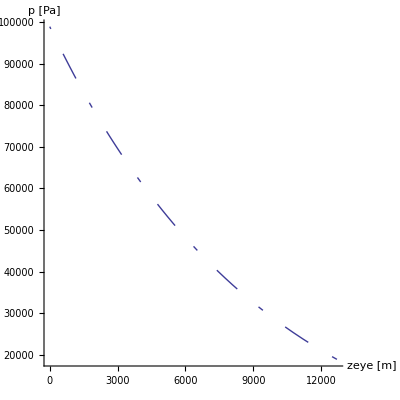

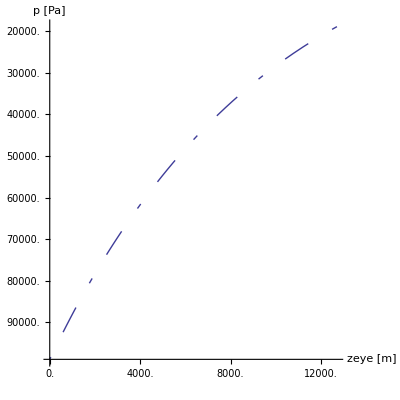

```mathematica
pze=ParametricPlot[Evaluate[{zeye[p],p}],{p,ptrop,peyes},AxesLabel->{"zeye [m]","p [Pa]"},AxesOrigin->{0,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.01,0.05,0.05,0.05}]}]
pze//ReverseY
```

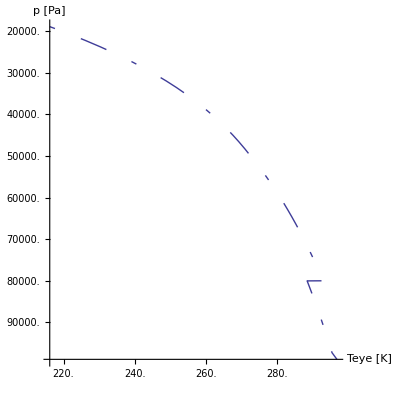

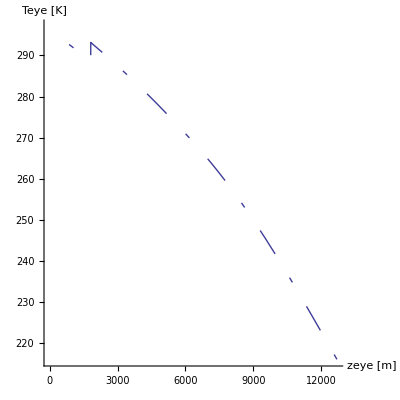

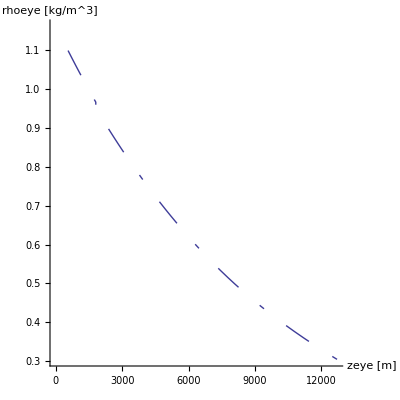

```mathematica
pte=ParametricPlot[Evaluate[{teye[p],p}],{p,peyes,ptrop},AxesLabel->{"Teye [K]","p [Pa]"},AxesOrigin->{200,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.01,0.05,0.05,0.05}]}];
pte//ReverseY

teze=ParametricPlot[Evaluate[{zeye[p],teye[p]}],{p,ptrop,peyes},AxesLabel->{"zeye [m]","Teye [K]"},AxesOrigin->{0,200},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.01,0.05,0.05,0.05}]}]

rhoeze=ParametricPlot[Evaluate[{zeye[p],rhoeye[p]}],{p,ptrop,peyes},AxesLabel->{"zeye [m]","rhoeye [kg/m^3]"},AxesOrigin->{0,0},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.01,0.05,0.05,0.05}]}]
```

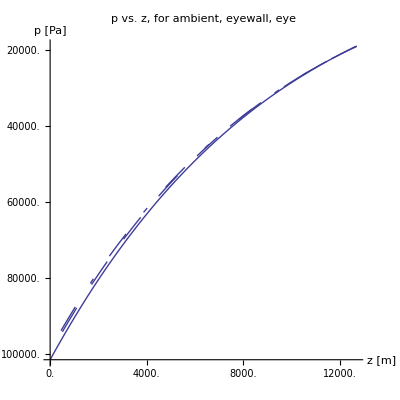

```mathematica
(* I am not exactly sure what you are trying to do here. *) 

Show[{pze,pzm,pza},AxesLabel->{"z [m]","p [Pa]"},PlotLabel->"p vs. z, for ambient, eyewall, eye",FormatType->TraditionalForm,AxesOrigin->{0,10000},AxesOrigin->{0,10000},PlotRange->All]//ReverseY
```

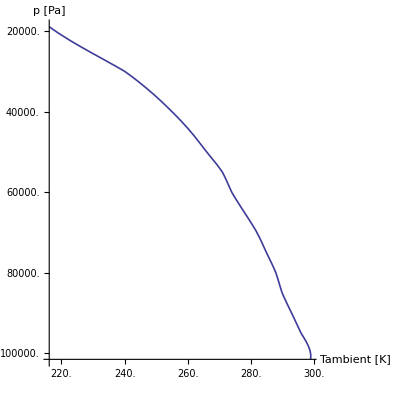

```mathematica
tap=ParametricPlot[Evaluate[{tamb[p],p}],{p,pambs,ptrop},AxesLabel->{"Tambient [K]","p [Pa]"},AxesOrigin->{175,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}],Thickness[0.003]}];
tap//ReverseY
```

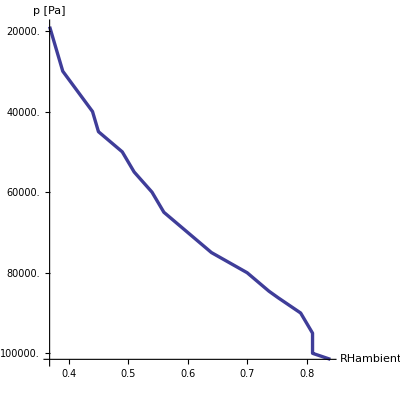

```mathematica
rhap=ParametricPlot[Evaluate[{rhamb[p],p}],{p,pambs,ptrop},AxesLabel->{"RHambient","p [Pa]"},AxesOrigin->{0,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}],Thickness[0.006]}];
rhap//ReverseY
```

```mathematica
tdewamb[p_]:=t/.FindRoot[(rhamb[p])*pvsat[tamb[p]]==pvsat[t],{t,tambs,200}]
```

FindRoot::nlnum: The function value {-3329.4683364835464` + 610.78` « 18 »^« 1 » TagBox[InterpolatingFunction[{{10000.`, 101500.`}}, {3, 3, 0, {17}, {2}, 0, 0, 0, 0}, {{10000.`, 20000.`, « 13 », 100000.`, 101500.`}}, « 1 », {Automatic}], False, Rule[Editable, False]][p]} is not a list of numbers with dimensions {1} at {t} = {299.`}.

ReplaceAll::reps: {FindRoot[rhamb[p] pvsat[tamb[p]] == pvsat[t], {t, tambs, 200}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

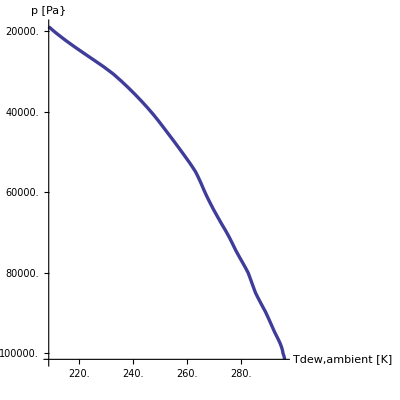

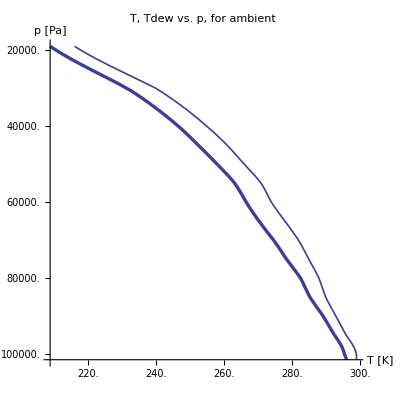

```mathematica
tdap=ParametricPlot[Evaluate[{tdewamb[p],p}],{p,pambs,ptrop},AxesLabel->{"Tdew,ambient [K]","p [Pa}"},AxesOrigin->{175,10000},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}],Thickness[0.006]}];
tdap//ReverseY

Show[{tap,tdap},AxesLabel->{"T [K]","p [Pa]"},PlotLabel->"T, Tdew vs. p, for ambient",FormatType->TraditionalForm,AxesOrigin->{175,10000},PlotRange->All] //ReverseY
```

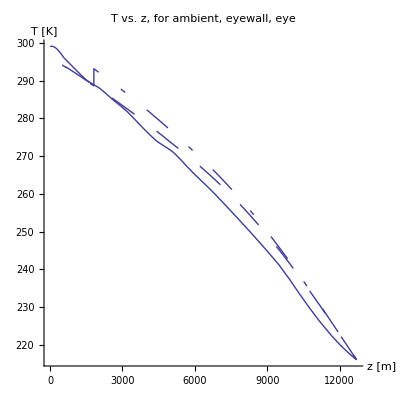

```mathematica
Show[{teze,tmzm,taza},AxesLabel->{"z [m]","T [K]"},PlotLabel->"T vs. z, for ambient, eyewall, eye",FormatType->TraditionalForm,AxesOrigin->{0,175},PlotRange->All]
```

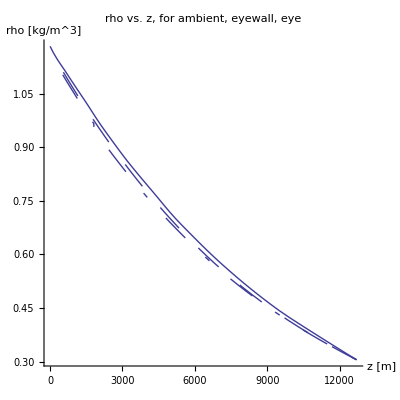

```mathematica
Show[{rhoeze,rhomzm,rhoaza},AxesLabel->{"z [m]","rho [kg/m^3]"},PlotLabel->"rho vs. z, for ambient, eyewall, eye",FormatType->TraditionalForm,AxesOrigin->{0,0},PlotRange->All]
```

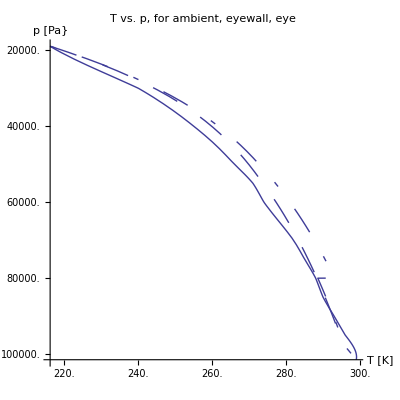

```mathematica
Show[{pte,ptm,pta},AxesLabel->{"T [K]","p [Pa}"},PlotLabel->"T vs. p, for ambient, eyewall, eye",FormatType->TraditionalForm,AxesOrigin->{200,10000},PlotRange->All]//ReverseY
```

```mathematica
vmaxts:=Sqrt[(pambs-pmoists)/((rhoambs+rhoeyes)/2)]
```

```mathematica
vmaxdh:=Sqrt[2(pambs-peyes)/((rhoambs+rhoeyes)/2)]
```

```mathematica
vmaxmh:=Sqrt[(pambs-peyes)/((rhoambs+rhoeyes)/2)]
```

```mathematica
vmaxh:=If[(pinterface<peyeds),vmaxmh,vmaxdh]
```

```mathematica
Print[StringForm["peak swirl,tropical storm = `` [m/s]; peak swirl, hurricane = `` [m/s]",Sequence@@(StandardForm/@{vmaxts,vmaxh})]]
```

peak swirl,tropical storm = StandardForm`37.84040419889448` [m/s]; peak swirl, hurricane = StandardForm`47.38127194813317` [m/s]

```mathematica
Print[StringForm["recall: pinterface = `` [Pa], peyeds = `` [Pa]",Sequence@@(StandardForm/@{pinterface,peyeds})]]
```

recall: pinterface = StandardForm`80000.` [Pa], peyeds = StandardForm`98532.88346042893` [Pa]

```mathematica
ttotamb[p_]:=tamb[p]+(9.8*zamb[p]/.sol[[1]])/1004+((2.5*10^6)*yamb[p])/1004;
```

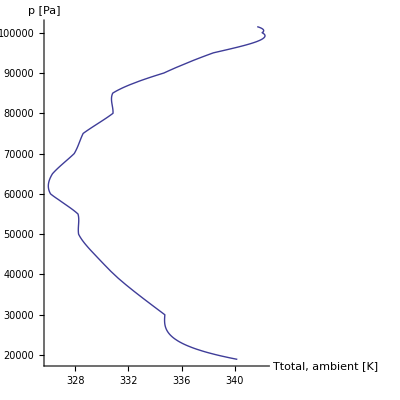

```mathematica
ptta=ParametricPlot[{ttotamb[p],p},{p,pambs,ptrop},AxesOrigin->{300,10000},AxesLabel->{"Ttotal, ambient [K]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{}]}]
```

```mathematica
ttotmoist[p_]:=(tmoist[p]/.solm[[1,2]])+((9.8)*(zmoist[p]/.solm[[1,1]])/1004)+((2.5*10^6)*ymoist[p])/1004;
```

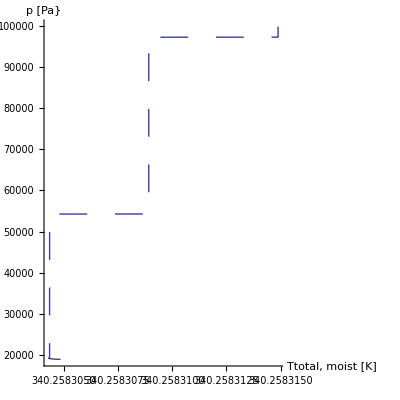

```mathematica
pttm=ParametricPlot[{ttotmoist[p],p},{p,pmoists,ptrop},AxesOrigin->{300,10000},AxesLabel->{"Ttotal, moist [K]","p [Pa}"},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.05,0.05}]}]
```

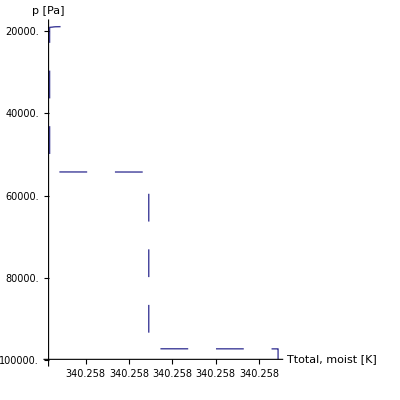

```mathematica
pttmr=ParametricPlot[{ttotmoist[p],p},{p,pmoists,ptrop},AxesOrigin->{300,10000},AxesLabel->{"Ttotal, moist [K]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.05,0.05}]}]//ReverseY
```

```mathematica
ttoteye[p_]:=teye[p]+((9.8*zeye[p]))/(1004)+((2.5*10^6)*yeye[p])/(1004);
```

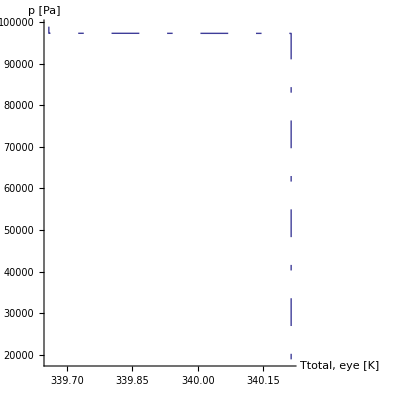

```mathematica
ptte=ParametricPlot[{ttoteye[p],p},{p,peyes,ptrop},AxesOrigin->{300,10000},AxesLabel->{"Ttotal, eye [K]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{Dashing[{0.01,0.05,0.05,0.05}]}]
```

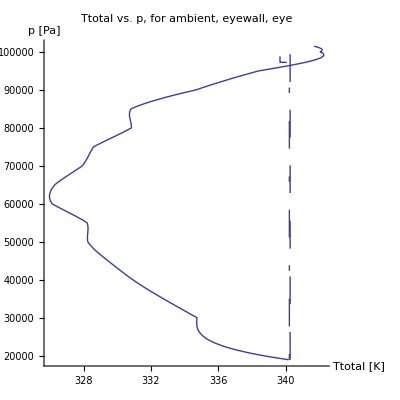

```mathematica
Show[{ptta,pttm,ptte},AxesLabel->{"Ttotal [K]","p [Pa]"},PlotLabel->"Ttotal vs. p, for ambient, eyewall, eye",FormatType->TraditionalForm,AxesOrigin->{300,10000},PlotRange->All,AspectRatio->1]
```